## normalized MRAC for unknown overall gain (Prob. 10.2)

System structure = underdamped oscillator, with G_0(s) = 1/(s^2+s+1)
used for book, Adaptive Control chapter, problem on normalized MRAC

```mathematica
Clear["Global`*"];
SetOptions[Plot,PlotRange -> All,Background->GrayLevel[0.97],PlotStyle->Thick];
```

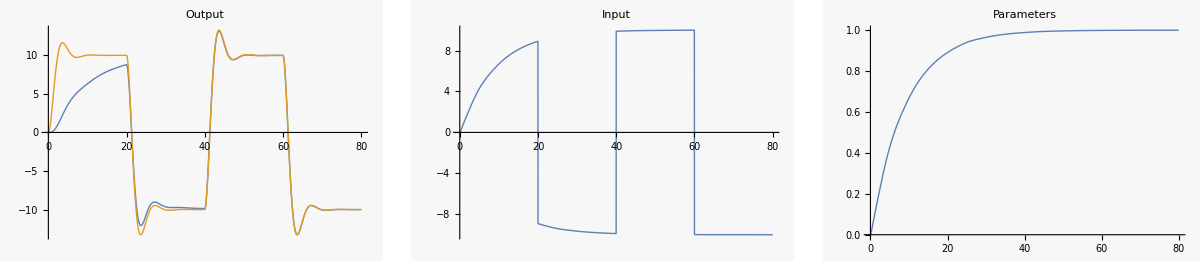

```mathematica
tend=80;
e[t]=y[t]-Subscript[y, m][t];                                         (* error *)
Subscript[u, c][t]=uc0 SquareWave[t/40];                  (* reference input *)
u[t]= θ[t]Subscript[u, c][t];                                           (* input to system *)

equations={
y''[t]+y'[t]+y[t]==k u[t], 
Subscript[y, m]''[t]+Subscript[y, m]'[t]+Subscript[y, m][t]==Subscript[k, m] Subscript[u, c][t],
θ'[t]==-γ (Subscript[y, m][t])/(α+(Subscript[y, m][t])^2)e[t]};
initialConditions={y[0]==y0,y'[0]==yd0,Subscript[y, m][0]==ym0,Subscript[y, m]'[0]==ymd0,θ[0]==θ0};

eqpars={γ->0.1,α->0.001,a->2,Subscript[a, m]->1,uc0->10,k->1,Subscript[k, m]->1}; 
initpars={y0->0,yd0->0,ym0->0,ymd0->0,θ0->0};

s=NDSolve[{equations/.eqpars,initialConditions/.initpars},
{y,Subscript[y, m],θ},{t,0,tend},MaxSteps->10^5];
u[t]=θ[t]Subscript[u, c][t]/.eqpars;  (* Re-evaluate for plot *)
udat=Evaluate[u[t]/.{s}]; ydat=Evaluate[y[t]/.s];
ymdat=Evaluate[Subscript[y, m][t]/.s]; θdat=Evaluate[θ[t]/.s];
p1=Plot[{ydat,ymdat},{t,0,tend},PlotLabel->Output];
p2=Plot[udat,{t,0,tend},PlotLabel->Input];
p3=Plot[θdat,{t,0,tend},PlotLabel->Parameters];
GraphicsRow[{p1,p2,p3},ImageSize->Full]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
dt=0.1;
ydat1=Table[ydat[[1]],{t,0,tend,dt}];     Export["ydat1.dat",ydat1];
ymdat1=Table[ymdat[[1]],{t,0,tend,dt}];   Export["ymdat1.dat",ymdat1];
udat1=Table[udat[[1]],{t,0,tend,dt}];     Export["udat1.dat",udat1];
thdat1=Table[θdat[[1]],{t,0,tend,dt}];    Export["thdat1.dat",thdat1];
*)
```